```mathematica
<<KerrGeodesics`
<<SpinWeightedSpheroidalHarmonics`
```

```mathematica
a=.998`32;
r0 = 10`32;
x = Cos[π/4`32];
Freqs=KerrGeoFrequencies[a,r0,0,x];
Ωθ=Freqs[[2]];
Ωϕ= Freqs[[3]];
orbit = KerrGeoOrbit[a,r0,0,x];
{t,r,θ,ϕ} = orbit["Trajectory"];
Υ = orbit["Frequencies"]["Υ_θ"];
Υϕ = orbit["Frequencies"]["Υ_ϕ"];
ℰ=orbit["Energy"];
ℒ=orbit["AngularMomentum"];
```

```mathematica
l=3;
m=1;

dtdλ[θ_]:= ℰ(((r0^2+a^2)^2)/(r0^2-2 r0+a^2)-a^2 Sin[θ]^2)+a ℒ(1-(r0^2+a^2)/(r0^2-2r0 +a^2))
ω = m Ωϕ + k Ωθ;

ut[θ_]:=-(4 a r0 ℒ)/((a^2+(-2+r0) r0) (a^2+2 r0^2+a^2 Cos[2 θ]))+(ℰ (a^4+2 r0^4+a^2 r0 (2+3 r0)+a^2 (a^2+(-2+r0) r0) Cos[2 θ]))/((a^2+(-2+r0) r0) (a^2+2 r0^2+a^2 Cos[2 θ]))

S = Table[SpinWeightedSpheroidalHarmonicS[0,l,m,a (m Ωϕ+k Ωθ)],{l,0,5},{m,-l,l},{k,-10,10}];
```

```mathematica
l=3;
m=1;


T = -(2 Ωθ r0)/(r0^2-2 r0 +a^2)Table[NIntegrate[(S[[l+1,l+m+1,11+k]][θ[λ],0])/ut[θ[λ]] Cos[m(Ωϕ t[λ]-ϕ[λ])+k Ωθ t[λ]]dtdλ[λ],{λ,0,(2π)/Υ},Method->"Trapezoidal",PrecisionGoal->10],{k,-10,10}];
```

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained -0.0000888928 and 5.46382×10^-9 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained -0.00010858 and 5.46553×10^-9 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in λ in the region {{0.,1.78664}}. NIntegrate obtained -0.0000973807 and 5.46703×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvi will be suppressed during this calculation.

```mathematica
T
```

{6.50462×10^-7,7.94521×10^-7,7.12571×10^-7,1.21666×10^-6,0.000109503,-4.05212×10^-6,-0.0391106,0.0000406525,0.210721,0.0000619887,0.0520217,0.0000656081,0.22621,0.0000524989,-0.00062834,4.67593×10^-6,4.41945×10^-6,1.8768×10^-6,1.34622×10^-6,1.02144×10^-6,8.01632×10^-7}

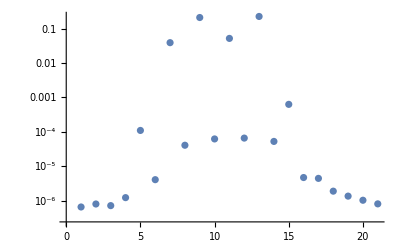

```mathematica
ListLogPlot@Abs[Flatten[T]]
```